# Defect Modular Bootstrap

## When the modular matrix has degeneracies modular bootstrap can only do so much to predict the the topological lines of the theory. Here we use a version of Breadth First Search to resolve the ambiguities.

## Modular Bootstrap

We will do this example on the folded Tricritical Ising CFT, but the parameters will be documented so that one can change them.

### Defining Folded Tricritical Ising Modular Data

c =   7/10

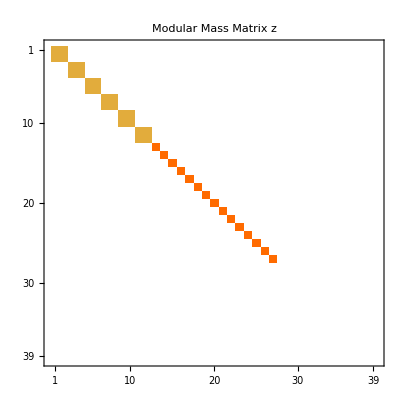

```mathematica
(* Define Tricritical Ising Parameters *)
p=5;
p'=4;
cv=1-6(p-p')^2/(p p')//Echo[#,"c = "]&;
hv[r_,s_]:=((p r - p' s)^2-(p - p')^2)/(4 p p');
sv[a_,b_]:=2 (2/(p p'))^(1/2)(-1)^(1 + a[[2]]b[[1]]+a[[1]] b[[2]])Sin[π p/p' a[[1]] b[[1]]]Sin[π p'/p a[[2]] b[[2]]] ;
tv[a_,e_:1]:=ⅇ^(2 π ⅈ e(hv[a[[1]],a[[2]]]-cv/24));
H=Join[Flatten[Table[{r, s}, {r, 1, Floor[(p'-1)/2]}, {s, 1, p-1}], 1], If[EvenQ[p'], Table[{p'/2, s}, {s, 1, Floor[(p-1)/2]}], {}]];
(* Labels of folded Tricritical Ising primaries under the fixed point chiral algebra *)
i=({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^#}& /@Range[2,2Length[H]+1])~Join~({#[[1]],#[[2]],0}&/@Subsets[H,{2}])~Join~({H[[Floor[#/2]]],H[[Floor[#/2]]],(-1)^# 2}& /@Range[2,2Length[H]+1]);
(* Their Conformal Weights *)
ho[a_]:=(hv@@(a[[1]])+hv@@(a[[2]])+a[[3]](a[[3]]-1)/2 + {{1,1},{1,1},-1}-a)(1-Abs[a[[3]]]-2)+((hv@@a[[1]])/2 +cv/24 3/2-(a[[3]]-2)/8 + {{1,1},{1,1},-2}-a)Abs[a[[3]]]-2//Simplify;
(* Modular T-Matrix *)
t=DiagonalMatrix[Exp[2π ⅈ(ho[#]-2 cv/24)]&/@i] // FullSimplify;
(* This is the ugliest way I can write down the s-matrix of this thing *)
sMaker[a_,b_]:= 
(sv[a[[1]],b[[1]]]sv[a[[2]],b[[2]]]+ sv[a[[1]],b[[2]]]sv[a[[2]],b[[1]]])a[[3]]b[[3]]+
sv[a[[1]],b[[1]]]sv[a[[2]],b[[1]]]a[[3]]Abs[b[[3]]]-1+
sv[a[[1]],b[[1]]]sv[a[[1]],b[[2]]]Abs[a[[3]]]-1 b[[3]]+ 
1/2 sv[a[[1]],b[[1]]]^2 Abs[a[[3]]]-1 Abs[b[[3]]]-1+
1/2 a[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-1 Abs[b[[3]]]-2+
1/2 b[[3]]sv[a[[1]],b[[1]]]Abs[a[[3]]]-2 Abs[b[[3]]]-1+
1/8 a[[3]]b[[3]]Total[(sv[a[[1]],#] tv[#]^2 sv[#,b[[1]]])&/@H]Exp[π ⅈ(hv@@(a[[1]]) + hv@@(b[[1]])-cv/12)]Abs[a[[3]]]-2 Abs[b[[3]]]-2;
s=FullSimplify[Array[sMaker[i[[#1]],i[[#2]]]&,{Length[i],Length[i]}],ComplexityFunction->LeafCount];
(* Modular Mass Matrix *)
z=Outer[(KroneckerDelta[#1,#2] + KroneckerDelta[#1[[1]],#2[[1]]]KroneckerDelta[#1[[2]],#2[[2]]]KroneckerDelta[#1[[3]],-#2[[3]]])(1-KroneckerDelta[Abs[#1[[3]]],2])(1-KroneckerDelta[Abs[#2[[3]]],2])&,i,i,1];
MatrixPlot[z,PlotLabel->"Modular Mass Matrix z"]
```

### Obtaining Modular Bootstrap Equations

```mathematica
SolveModularBootstrap[z_,s_]:=Module[
{X,x,nz, st=ConjugateTranspose[s],m,coeff,A, eqn,multipliers,basis},
Needs["math4ti2`"];

(* Get Nonzero positions on the Mass Matrix and replace them with variables *)
nz=Position[z, _?(# !=0 &)];
X=Array[x,Length[nz]];
m=st. ReplacePart[z,Thread[nz->X]] . s//Flatten;

(* Extract the coefficients for each variable in the S transformed Mass Matrix *)
coeff= CoefficientArrays[m,X][[2]]//Normal//N//Chop;

(* Pick the maximum number of independent equations and invert them *)
A=Chop@Inverse@N@coeff[[Flatten[FirstPosition[#,1]&/@DeleteCases[Chop@RowReduce@N@Transpose@coeff,{0..}]]]];

(* Plug them back in to the S-Transformed Modular Matrix to obtain constraints *)
m=Chop[N[coeff.A]].X;
A=RootApproximant[A];
eqn=DeleteDuplicates@Rationalize@Chop@Expand[#>=0&/@m];

(* Rescale any variables that need it so that the system has integer coefficients *)
multipliers=Min@Cases[eqn,(a_.*#)>=0:>a]^-1&/@X;
eqn=(#[[0]][Subtract@@#//ExpandAll,0])&/@(eqn/. Thread[X->multipliers*X]);

(* Use Z-Solve to find a basis of simple objects *)
basis =math4ti2`zsolve[eqn][[2]];

A. (multipliers*#)&/@basis //FullSimplify
];
families=Sort[SolveModularBootstrap[z,s],#1[[1]] <= #2[[1]]&];
families//Transpose//MatrixForm
noninvertibleFamilies=Select[families,#[[1]]!=1&];
```

math4ti2: Mathematica interface to 4ti2 (http://www.4ti2.de/)
Copyright (C) 2017, Ralf Hemmecke <ralf@hemmecke.org>
Copyright (C) 2017, Silviu Radu <sradu@risc.jku.at>

(1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | √(7+3 √5) | √(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) |  | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | (-3+√5)/(√2) | (-3+√5)/(√2) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | 2 √(5-√5) | 2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | √(10-2 √5) | √(10-2 √5) | 3-√5 | -2 √(5-√5) | 2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(10-4 √5) | -2 √(10-4 √5)
1 | 1 | 1 | -1 | -1 | √2 | √2 | -√2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 2 |  |  |  |  | √(3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | √(10-2 √5) | √(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | 2 √(5-√5) | -2 √(5-√5) | -2 √(5-2 √5) | -2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | -2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | √2 | √2 | √2 | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (1-√5) | 2 |  |  |  |  |  | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (3-√5) | 1-√5 | √(7-3 √5) | √(7-3 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | -√(10-2 √5) | 3-√5 | -2 √(5-√5) | -2 √(5-√5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(5-2 √5) | 2 √(10-4 √5) | 2 √(10-4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | -2 √(5+√5) | -2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | √(2 (5+√5)) | √(2 (5+√5)) | 3+√5 | 2 √(5+√5) | -2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(5+2 √5) | 2 √(10+4 √5) | -2 √(10+4 √5)
1 | 1 | 1 | -1 | -1 | -√2 | -√2 | √2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | √(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | √(2 (5+√5)) | √(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | -2 √(5+√5) | 2 √(5+√5) | 2 √(5+2 √5) | 2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | 1 | 1 | 1 | -√2 | -√2 | -√2 | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (1+√5) | 2 | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | -√(3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (3+√5) | 1+√5 | -√(7+3 √5) | -√(7+3 √5) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | -√(2 (5+√5)) | 3+√5 | 2 √(5+√5) | 2 √(5+√5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | -2 √(5+2 √5) | 2 √(10+4 √5) | 2 √(10+4 √5)
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | √(5+√5) | -√(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | √(5+√5) | -√(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | -√(10+4 √5) | √(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1-√5) | 1/2 (1+√5) | 1/2 (1+√5) | 1/2 (-1-√5) | 1/2 (-1-√5) | 1/2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3+√5) | 1/2 (3+√5) | 1/2 (-3-√5) | 0 | 0 | 0 | -√(5+√5) | √(5+√5) | -√(5+√5) | √(5+√5) | 0 | 0 | 0 | √(10+4 √5) | -√(10+4 √5) | -√(10+4 √5) | √(10+4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | √(5-√5) | -√(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | 0 | 0
1 | 1 | -1 | -1 | 1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | √(5-√5) | -√(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | √(10-4 √5) | -√(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
1 | 1 | -1 | 1 | -1 | 0 | 0 | 0 | 1/2 (-1+√5) | 1/2 (1-√5) | 1/2 (1-√5) | 1/2 (-1+√5) | 1/2 (-1+√5) | 1/2 (1-√5) | 0 | 0 | 0 | 0 | 0 | 0 | 1/2 (3-√5) | 1/2 (3-√5) | 1/2 (-3+√5) | 0 | 0 | 0 | -√(5-√5) | √(5-√5) | -√(5-√5) | √(5-√5) | 0 | 0 | 0 | -√(10-4 √5) | √(10-4 √5) | √(10-4 √5) | -√(10-4 √5) | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | √10 | -√10 | -√10 | √10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 2 √2 | 2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | √2 | √2 | √2 | √2 | 0 | -2 | -2 | -2 | 2 | -2 √2 | -2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1+√5 | 1+√5 | 1+√5 | 1+√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3+√5 | 3+√5 | 3+√5 | -2 (1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | -2 (3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | √(3+√5) | -√(3+√5) | √(3+√5) | -√(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | -√(7+3 √5) | √(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | √(3+√5) | √(3-√5) |  | -√(3+√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1-√5 | 1-√5 | 1-√5 | 1-√5 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 3-√5 | 3-√5 | 3-√5 | 2 (-1+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 2 (-3+√5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | -2 √2 | -2 √2 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 4 | -√2 | -√2 | -√2 | -√2 | 0 | -2 | -2 | -2 | 2 | 2 √2 | 2 √2 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 | √(3-√5) | √(3+√5) | -√(3+√5) |  | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 | √(3-√5) |  | √(3-√5) |  | 0 | -3+√5 | 3-√5 | 0 | 0 | √(7-3 √5) | (-3+√5)/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | -4 | -√10 | √10 | √10 | -√10 | 0 | -2 | -2 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | -√5 | 1 | -1 | √5 | 0 | 0 | 0 |  | -√(3+√5) | √(3+√5) | √(3-√5) | 0 | 2 | -2 | 0 | 0 | √2 | -√2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | √2 | -√2 | 0 | 0 | 1-√5 | -1+√5 | 0 | 0 | 0 | 0 |  | √(3-√5) |  | √(3-√5) | 0 | -3+√5 | 3-√5 | 0 | 0 | (-3+√5)/(√2) | √(7-3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | 0 | 1+√5 | -1-√5 | 0 | 0 | 0 | 0 | -√(3+√5) | √(3+√5) | -√(3+√5) | √(3+√5) | 0 | -3-√5 | 3+√5 | 0 | 0 | √(7+3 √5) | -√(7+3 √5) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | -2 | 0 | 0 | 0 | -√2 | √2 | 0 | √5 | 1 | -1 | -√5 | 0 | 0 | 0 | -√(3+√5) |  | √(3-√5) | √(3+√5) | 0 | 2 | -2 | 0 | 0 | -√2 | √2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## Resolving Ambiguities

As we can see from the answers above for part of the primaries the action of the defects is ambiguous and we really only know the trace. Yet we have a lot of data, perhaps enough to fully constrain the action on the primaries (up to a basis choice). To do this we will use fusion rules. These are highly constrained also simply by looking at the action in the nondegenerate primaries. Then we will search fusion rules for consistencies using a version of BFS.

### Defect Manipulations

Since we don’t need a really big matrix to store the action of the defects, we will instead opt to store them using a list of 1x1 and 2x2 matrices depending on which are ambiguous or not. So we can define an associative operation for the tensor product!!

```mathematica
(* Define a Defect Fusion Product Operation *)
SetAttributes[CircleTimes,{Flat,OneIdentity}]
a_ ⊗ b_:=Which[MatrixQ[#[[1]]]&&MatrixQ[#[[2]]],#[[1]].#[[2]],True,#[[1]]*#[[2]]]&/@Transpose[{a,b}];
CircleTimes[a_,b_,rest__]:=CircleTimes[CircleTimes[a,b],rest]

(* A couple of helper functions that can be applied to Lines *)
tr[x_]:=Which[MatrixQ[x],Tr[x],True,x];
inv[x_]:=Which[MatrixQ[x],Inverse[x],True,1/x];
dual[x_]:=Which[MatrixQ[x],ConjugateTranspose[x],True,Conjugate[x]];
SuperDagger[x_]:=dual/@x;
ShowLine[L_]:=MatrixForm[MatrixForm/@L];

SetAttributes[Time,HoldFirst]
Time[x_]:=With[{res=AbsoluteTiming[x]},Echo[res[[1]],"Time: "];res[[2]]];

(* This mask tells us if the current primary is degenerate *)
degMask=Thread[families[[1]]!=1];
degPos=Flatten@Position[degMask,True];
nondegPos=Flatten@Position[Not/@degMask,True];
deg[x_]:=degMask[[x]];
degNum=Total@Boole@degMask;
primNum=Total@Boole@degMask;
famNum=Length@families;
familiesNondeg=families[[All,nondegPos]];
```

### Invertible Lines

```mathematica
GetInvertibleLines[]:=Module[
{i={{1,0},{0,1}},
a={{1,0},{0,-1}},
b={{0,1},{1,0}},
c={{0,1},{-1,0}},
L1,Lσ,Lχ},
L1={1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,i,i,i,i,i,i,i,i,i,i,i,i,i,i,i};
Lσ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,a,a,a,a,a,a,a,a,a,a,a,a,a,a,a};
Lχ={1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,a,a,a,c,c,a,a,c,c,a,c,c,c,c,-a};
{L1,Lχ⊗Lχ,Lχ⊗Lσ,Lσ⊗Lχ,Lσ,Lσ⊗Lχ⊗Lχ,Lχ,Lχ⊗Lχ⊗Lχ}
];

(* Extract the invertible Lines *)
Li=GetInvertibleLines[];
solvedFamilies=<|
1->{Li[[1]]},
2->{Li[[2]]},
3->Li[[3;;4]],
4->Li[[5;;6]],
5->Li[[7;;8]]
|>;
SolvedQ[x_Integer]:=KeyExistsQ[solvedFamilies,x];

(* Obtain a general Gauge Transformation that preserves the invertible Lines *)
Lp=Array[Which[!deg[#],1,deg[#],{{P[#,1] ,P[#,2] },{P[#,3],P[#,4]}}]&,famNum];
Lp=(Lp //.{ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@Li]==0],Backsubstitution->True]]})[[1]];
Lpp=Lp//Variables;
(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
invertibleLp=(Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@Lp)])
},
invertibleLp=invertibleLp/.Thread[Lpp->vars];
LpInvertibleQ:=Function@@{vars,Simplify[Evaluate[invertibleLp]]}];

(* These are Queries for if a line is related by conjugation of invertible defects, or by a change of Gauge, or both *)
productOrbit[x_]:=productOrbit[x]=Simplify[#[[1]]⊗x⊗#[[2]]]&/@Tuples[{Li,Li}];
conjugateOrbit[x_]:=conjugateOrbit[x]=Rationalize@N[#⊗x⊗(inv/@#)]&/@Li;
ConjugateOrbitQ[x_,y_]:=MemberQ[conjugateOrbit[x],Rationalize@N[y]];
leftOrbit[x_]:=leftOrbit[x]=Rationalize@N[#⊗x]&/@Li;
LeftOrbitQ[x_,y_]:=MemberQ[leftOrbit[x],Rationalize@N[y]];
rightOrbit[x_]:=rightOrbit[x]=Rationalize@N[x⊗#]&/@Li;
RightOrbitQ[x_,y_]:=MemberQ[rightOrbit[x],Rationalize@N[y]];
OrbitQ[x_,y_]:=Or[RightOrbitQ[x,y],LeftOrbitQ[x,y],ConjugateOrbitQ[x,y]];
(* Calculates the nullspace of the Jacobian of Lp x - x Lp, and if it is empty then there is no gauge transformation *)
Clear[gaugeNullSpace];
gaugeNullSpace[x_,y_]:=gaugeNullSpace[x,y]=NullSpace@Outer[D,Flatten[ExpandAll[Lp⊗x-y⊗Lp]],Lpp];
GaugeQ[x_,y_]:=Module[
{ns=gaugeNullSpace[x,y],dummies},

Which[
ns==={},False,
Length@ns ===Length@Lpp,True,
True,
dummies=Array[x,Length@ns];
Assuming[Thread[Variables[{x,y,dummies}]!=0],Simplify[LpInvertibleQ@@(dummies.ns)]]
]];
(* Combines all queries *)
OrbitGaugeQ[x_,y_]:=OrbitQ[x,y]||GaugeQ[x,y];

(* Returns conditions for line x to be related to line y by a valid gauge transformation *)
FindGaugeRelations[x_,y_]:=Reduce[And@@(Thread[Flatten[N[Lp⊗x - y⊗Lp]]==0]~Join~Thread[Lpp!=0]),Lpp,Complexes,Backsubstitution->True];
```

### Search Fusion Rules

Since we can obtain some partial information for the fusion rules among defects belonging to each family we can extract and list them in the following

```mathematica
(* Takes a matrix M and a vector v and finds all possible nonnegative integer combinations of rows of M that sum to v *)
FindIntegerCombinations[M_,v_]:=Module[
{n=Length[M],m=Length[v],MT=Transpose[N[M]],ubounds, enumerate,results={}},

(* Use linear programming to estimate the maximum number a row can be added in a solution for v *)
ubounds=Table[Module[{sol},
sol=Quiet[LinearProgramming[-UnitVector[n,i],MT,Transpose[{N[v],ConstantArray[0,m]}],ConstantArray[0,n]]];
If[VectorQ[sol],Max[0,sol[[i]]//Chop//RootApproximant],sol]]
,{i,n}];

(* Explore the rest recursively until you hit zero *)
enumerate[rem_,idx_,current_]:=Which[idx>n,If[Chop[N[rem]]==ConstantArray[0,m],AppendTo[results,current]],True,Do[enumerate[rem-k*M[[idx]],idx+1,Append[current,k]],{k,0,ubounds[[idx]]}]];
enumerate[v,1,{}];
results
];
Clear[FindIntegerCombinationsCached];
FindIntegerCombinationsCached[M_,v_]:=FindIntegerCombinationsCached[M,v]=FindIntegerCombinations[M,v];

(* Store maximum possible fusion pathways between families *)
(*fusionPathways=ParallelArray[FindIntegerCombinations[familiesNondeg//N,familiesNondeg[[#1]]*familiesNondeg[[#2]]//N]&,{famNum, famNum}];*)
```

### Constrain Using Invertible Defect Fusion

Use fusion rules with invertible defects to constrain the possible candidates for lines in a family up to fusion by invertible and gauge transformations

```mathematica
(* Functions to create a defect with free variables and given traces, as well to extract the variables *)
l[traces_,var_]:= Array[Which[!deg[#],traces[[#]],deg[#],{{var[#,1] ,var[#,2] },{var[#,3],traces[[#]]-var[#,1]}}]&,Length@traces];
getVars[x_]:=x//Flatten//Variables;

(* Solves system quietly ignoring the cases when parameters are undetermined *)
(*QuietSolve[eqn_,vars_]:=Quiet[Solve[eqn/. a_?InexactNumberQ:>Rationalize[a],vars],{Solve::svars,Solve::fulldim}];*)
QuietSolve[eqn_,vars_]:=Quiet[Solve[eqn,vars],{Solve::svars,Solve::fulldim,Solve::ratnz}];

(* Cleans up some variables *)
CanonicalizeVars[list_]:=Array[i|->Module[{vars},
vars=getVars@list[[i]];
list[[i]]/.MapIndexed[#->#[[0]][i,#2[[1]]]&,vars]],
Length@list];

(* Given a defect with free variables, it outputs a list of the variables that are pure gauge *)
GaugeParams[x_]:=Module[
{vars=getVars@x},
Pick[vars,Simplify[GaugeQ[x,x/. #->z]&/@vars,Assumptions->Flatten[{Thread[vars!=0],z!=0}]]]
];
AllGaugeQ[x_]:=Flatten[First/@BooleanVariables[FunctionDomain[Flatten[x],Variables[x]]]]===Flatten[GaugeParams[x]];

(* Provide candidates for the representation of a defect line up to fusion with invertible lines and gauge transformation *)
ConstrainWithInvertibles[traces_,var_]:=Module[
{ defect=l[traces,var],vars,products,fusions,result},
vars=getVars[defect];
SetAttributes[var,NHoldAll];

(* Calculate the possible fusion channels with the invertible defects *)
(*products=(#⊗defect)&/@Li;*)
products=productOrbit[defect]//DeleteDuplicates;
fusions=MapThread[{N[tr/@#1],FindIntegerCombinationsCached[familiesNondeg,#2[[nondegPos]]]}&,{products,products}]//DeleteDuplicates;
fusions=Transpose[{fusions[[All,1]],N[#.families]&/@#}]&/@Tuples[fusions[[All,2]]];
 
(* Convert to equations for their traces, then solve and plug back in *)
fusions=Map[Flatten[MapThread[Equal]/@#,1]&,fusions];
result=Flatten[DeleteCases[((defect//.#)&/@(QuietSolve[#,vars]))&/@fusions,{}],1];

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitGaugeQ]
];
```

### Constrain Using Consistency with Themselves.

We now have candidates for each family constrained by consistency with fusion with invertible lines. The next step would be to constrain the parameters with respect to their fusion and the fusion with their orientation reversal (aka dual).

```mathematica
(* Returns which column indices have no variables *)
noVars[table_]:=Pick[Range[Length@First@table],VectorQ[#,NumericQ]&/@Transpose[table]];

(* Constrain using fusion with their dual *)
ConstrainWithDualFusion[defects_]:=Module[
{vars=Variables[defects],products,indices,fusions,result},

(* Calculate Fusion among members of family *)
products=DeleteDuplicates@Flatten[{(tr/@(#⊗ SuperDagger[#]-Li[[1]])),(tr/@(SuperDagger[#]⊗ #-Li[[1]]))}&/@defects,1];
indices=noVars[products];

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
fusions=MapThread[{N[tr/@#1],FindIntegerCombinationsCached[families[[All,indices]],#2[[indices]]]}&,{products,products}]//DeleteDuplicates;
fusions=Transpose[{fusions[[All,1]],N[#.families]&/@#}]&/@Tuples[fusions[[All,2]]];

(* Solve and prettify *)
fusions=Map[Flatten[MapThread[Equal]/@#,1]&,fusions];
result =Flatten[(defects//.#)&/@DeleteCases[(QuietSolve[#,vars]),{}]&/@fusions,2];
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
DeleteDuplicates[FullSimplify@result,OrbitGaugeQ]
];

(* Take a collection of candidate lines for a family and use their self fusion to further constrain them *)
ConstrainWithSelfFusion[defects_]:=Module[
{vars=Variables[defects],products,indices,fusions,result},

(* Calculate Fusion among members of family *)
products=((tr/@(#[[1]]⊗#[[2]]))&/@Tuples[{defects,defects}]);
indices=noVars[products];

(* Constrain their possible fusion pathways and turn them into equations using their traces *)
fusions=MapThread[{N[tr/@#1],FindIntegerCombinationsCached[families[[All,indices]],#2[[indices]]]}&,{products,products}]//DeleteDuplicates;
fusions=Transpose[{fusions[[All,1]],N[#.families]&/@#}]&/@Tuples[fusions[[All,2]]];
fusions=Map[Flatten[MapThread[Equal]/@#,1]&,fusions];

(* Solve and prettify *)
result =Flatten[(defects//.#)&/@DeleteCases[(QuietSolve[#,vars]),{}]&/@fusions,2];
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
DeleteDuplicates[FullSimplify@result,OrbitGaugeQ]
];

ConstrainWithSelfFusion[defects_]:=Module[{vars=Variables[defects],n=Length[defects],SolveForSubset,queue,visited,maximalResults,current,sol,newChildren},(*Refactor the solve logic to work on an arbitrary subset of defect indices*)SolveForSubset[indices_]:=Module[{subset=defects[[indices]],products,noVarIdx,fusions,result},products=(tr/@(#[[1]]⊗#[[2]]))&/@Tuples[{subset,subset}];
noVarIdx=noVars[products];
fusions=MapThread[{N[tr/@#1],FindIntegerCombinationsCached[families[[All,noVarIdx]],#2[[noVarIdx]]]}&,{products,products}]//DeleteDuplicates;
(*Early exit:if any product has no valid fusion channel the whole subset is inconsistent*)If[AnyTrue[fusions[[All,2]],#==={}&],Return[{}]];
fusions=Transpose[{fusions[[All,1]],N[#.families]&/@#}]&/@Tuples[fusions[[All,2]]];
fusions=Map[Flatten[MapThread[Equal]/@#,1]&,fusions];
result=Flatten[(subset//.#)&/@DeleteCases[QuietSolve[#,vars],{}]&/@fusions,2];
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
DeleteDuplicates[FullSimplify@result,OrbitGaugeQ]];
(*BFS:start from the full set and shrink by one on failure.A subset is "maximal consistent" if it solves but none of its supersets (already visited) did.*)queue={Range[n]};
visited={};
maximalResults={};
While[queue=!={},current=First[queue];
queue=Rest[queue];
(*Skip if already explored*)If[MemberQ[visited,current],Continue[]];
AppendTo[visited,current];
sol=SolveForSubset[current];
If[sol=!={},(*Consistent:record solutions for this subset*)AppendTo[maximalResults,sol],(*Inconsistent:enqueue all subsets with one element removed*)newChildren=Sort/@(Delete[current,{{#}}]&/@Range[Length[current]]);
newChildren=Select[newChildren,!MemberQ[visited,#]&];
queue=DeleteDuplicates@Join[queue,newChildren]]];
(*Flatten and deduplicate across all maximal consistent subsets*)DeleteDuplicates[Flatten[maximalResults,1],OrbitGaugeQ]];
```

```mathematica
res=ConstrainWithInvertibles[families[[15]],x]//Time;
ShowLine/@res;
res=ConstrainWithDualFusion[res]//Time;
Which[Variables[res]==={},Echo["No Third step"];ShowLine/@res,
True,
res=ConstrainWithSelfFusion[res]//Time;
Echo[And@@(AllGaugeQ/@res),"All gauge?: "];
ShowLine/@res
]
```

Time:   0.217002

Time:   0.05359

No Third step

{(2
2
2
2
2
2
2
2
2
2
2
2
2
2
2
2
0
0
0
0
0
0
0
0
(-2 | 0
0 | -2)
(2 | 0
0 | 2)
(-2 | 0
0 | -2)
(0 | 0
0 | 0)
(0 | 0
0 | 0)
(-2 | 0
0 | -2)
(2 | 0
0 | 2)
(0 | 0
0 | 0)
(0 | 0
0 | 0)
(-2 | 0
0 | -2)
(0 | 0
0 | 0)
(0 | 0
0 | 0)
(0 | 0
0 | 0)
(0 | 0
0 | 0)
(0 | 0
0 | 0))}

# Automatic Bootstrap

Now we have the building blocks to do the pruning for the entire family of fusion rules. The only things we need to figure out now are:
1. Keeping track of gauge degrees of freedom efficiently
2. Updating Gauge Transformation based on the current solved defects.
3. Keep track of the growing collection of defect lines.

## Structures to keep track of the problem

```mathematica
(* A collection of all solved defects in the theory *)
L=GetInvertibleLines[];(*~Join~(res/.Thread[Variables[res]->Table[Unique["x"],Length@Variables@res]]);*)

(* Automatic Gauge Transformations *)
gaugeVars= getVars[L];
gaugeVarRules=Thread[gaugeVars!=0];
GetGeneralGaugeTransform[L_,gaugeVars_,gaugeVarRules_,var_:P]:=Module[{Lp,LpInvertibleQ,Lpp},
(* Build a General Gauge Transformation *)
Lp=Array[Which[!deg[#],1,deg[#],{{var[#,1] ,var[#,2] },{var[#,3],var[#,4]}}]&,famNum];
Lp=(Lp //.{Assuming[gaugeVarRules,ToRules[Reduce[And@@Thread[Flatten[(Lp⊗# -#⊗Lp)&/@L]==0],Backsubstitution->True]]]});
Lpp=DeleteElements[Variables[Lp],gaugeVars];

(* Checks if Lp is invertible for a given numerical set of P variables *)
Module[{
vars=Table[Unique["p"],Length@Lpp],
varsg=Table[Unique["g"],Length@gaugeVars],
invertibleLp=And@@((Simplify@Not@Reduce[Or@@(Which[MatrixQ[#],Det[#]==0,True,#==0]&/@#)])&/@Lp)
},
invertibleLp=invertibleLp/.Thread[Lpp->vars]/.Thread[gaugeVars->varsg];
	Echo[invertibleLp];
LpInvertibleQ:=Function@@{vars,Assuming[gaugeVarRules/.Thread[gaugeVars->varsg],Simplify[Evaluate[invertibleLp]]]}
];
{Lp,Lpp,LpInvertibleQ}
];

(* Calculate Conjugate Orbit *)
Clear[conjugateOrbitS];
conjugateOrbitS[x_,Li_:Li,gaugeVarRules_:gaugeVarRules]:=conjugateOrbitS[x,Li,gaugeVarRules]=DeleteDuplicates[Simplify[#⊗x⊗(inv/@#),Assumptions->gaugeVarRules]&/@Li];
```

## Solving with Existing Lines

As we keep going through families with higher and higher quantum dimension we can use existing lines to constrain new ones. This is a variation of constrain with invertible lines, but this time it uses the full might of the already solved families. We will do an extra optimization. Since once a family is solved we know all the lines there and not just the traces,  this places a much stricter constraint on what the results of fusions can be other than their traces.

```mathematica
(* Calculate the orbit of the new line under fusion using the defects that we already know *)
Clear[fusionOrbit];
fusionOrbit[x_,L_:L,gaugeVarRules_:gaugeVarRules]:=fusionOrbit[x,L,gaugeVarRules]=DeleteDuplicates[Simplify[Flatten[Outer[#1⊗x⊗#2&,L,L,1,1],1],Assumptions->gaugeVarRules]];

(* Find possible integer combinations for a defect with unknown variables *)
PossibleSimpleDecompositions[trace_,gaugeVars_:gaugeVars]:=Module[
{vars=Variables[trace],indices},
Which[
Length[vars]==0,
FindIntegerCombinationsCached[families,trace],
True,
indices=Flatten@Position[trace, _?(FreeQ[#,Alternatives@@vars]&),{1},Heads->False];
FindIntegerCombinationsCached[families[[All,indices]],trace[[indices]]]
]
];

(* Uses trace equations and known lines to produce candidates for the unknown parameters *)
ReduceDecompositions[defect_,trace_,decompositions_]:=Or@@(decomp|->Module[
{sparseDecomp=SparseArray[decomp],indices,sol},
indices=sparseDecomp["NonzeroPositions"][[All,1]];
Which[
(* If the fusion is in one family and it has been solved equate them cell by cell *)
And[Length[indices]==1,SolvedQ[indices[[1]]]],
Reduce[Or@@(And@@DeleteCases[MapThread[Equal,{Flatten[defect],Flatten[#]}],True]&/@solvedFamilies[indices[[1]]])],
(* Otherwise equate their traces *)
True,
Reduce[And@@DeleteCases[MapThread[Equal,{trace,decomp.families},1],True]]
]])/@decompositions;


ConstrainWithKnown[defect_,var_:x,L_:L,gaugeVars_:gaugeVars,gaugeVarRules_:gaugeVarRules]:=Module[
{vars=Variables[defect],products,traces,decompositions,result},

(* Calculate the possible fusion channels with the known defects *)
products=fusionOrbit[defect,L,gaugeVarRules];
traces=N[tr/@#&/@products];
decompositions=PossibleSimpleDecompositions/@traces;


(* Obtain a system of equations and reduce it *)
decompositions=MapThread[ReduceDecompositions,{products, traces, decompositions}];
result=(defect//.#)&/@(QuietSolve[decompositions,vars]);

(* Convert numerical constants back to algebraic form, preserving variables *)
result=result/. a_?NumericQ/;!IntegerQ[a]:>RootApproximant[a,4];
CanonicalizeVars@DeleteDuplicates[Simplify@result,OrbitGaugeQ]
];
```

```mathematica
SetAttributes[x,NHoldAll];
def=l[families[[6]],x];
decomps=ConstrainWithKnown[def]//Time;
ShowLine/@decomps
```

Time:   0.382329

{(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[1,1]
x[1,2] | 0)
(√2 | x[1,3]
x[1,4] | √2)
(0 | x[1,5]
x[1,6] | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(0 | x[1,7]
x[1,8] | 0)
(-√2 | x[1,9]
x[1,10] | -√2)
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | x[1,11]
x[1,12] | 0)
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(1/(√2) | 1/(√2)
1/(√2) | 1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(-1/(√2) | -1/(√2)
-1/(√2) | -1/(√2))
(0 | x[1,13]
x[1,14] | 0)),(√2
√2
√2
√2
-√2
-√2
-√2
-√2
√2
√2
√2
√2
-√2
-√2
-√2
-√2
0
0
0
0
0
0
0
0
(0 | x[2,1]
x[2,2] | 0)
(√2 | x[2,3]
x[2,4] | √2)
(0 | x[2,5]
x[2,6] | 0)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(0 | x[2,7]
x[2,8] | 0)
(-√2 | x[2,9]
x[2,10] | -√2)
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | x[2,11]
x[2,12] | 0)
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(1/(√2) | -1/(√2)
-1/(√2) | 1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(-1/(√2) | 1/(√2)
1/(√2) | -1/(√2))
(0 | x[2,13]
x[2,14] | 0))}